```mathematica
DSolve[{D[a[t],t,t]-a[t]^2==0},a,t]
```

{{a→Function[{t},6^(1/3) WeierstrassP[(t+C[1])/6^(1/3),{0,C[2]}]]}}

```mathematica
b=FullSimplify[a[t]/.%]
```

{6^(1/3) WeierstrassP[(t+C[1])/6^(1/3),{0,C[2]}]}

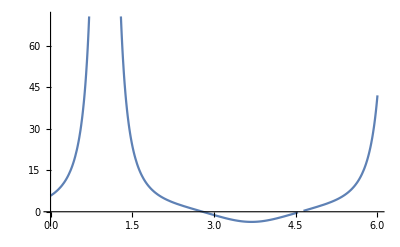

```mathematica
Plot[b/.{C[1]->-1}/.{C[2]->-33},{t,0,6},PlotRange->Automatic]
```

```mathematica
NSolve[b==0/.{C[1]->-1}/.{t->0},C[2]]
```

NSolve[{6^(1/3) WeierstrassP[1/6^(1/3),{0,C[2]}]}==0,C[2]]

```mathematica
Series[b,{t,0,3}]
```

{6^(1/3) WeierstrassP[C[1]/6^(1/3),{0,C[2]}]+WeierstrassPPrime[C[1]/6^(1/3),{0,C[2]}] t+(3^(2/3) WeierstrassP[C[1]/6^(1/3),{0,C[2]}]^2 t^2)/2^(1/3)+(2^(1/3) WeierstrassP[C[1]/6^(1/3),{0,C[2]}] WeierstrassPPrime[C[1]/6^(1/3),{0,C[2]}] t^3)/3^(2/3)+O[t]^4}